```mathematica
(* Reference:M.M.Shepherd and J.G.Laframboise Mathematics of Computation, v36, p249 (1981) *)
```

```mathematica
g[x_]:=(1+2x)Exp[x^2]Erfc[x]
```

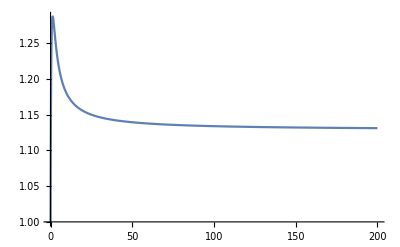

```mathematica
Plot[g[x],{x,0,200},PlotRange->All,WorkingPrecision->20]
```

```mathematica
k0=15/4;
F[t_]:=g[k0(1+t)/(1-t)]
m=30;
t=Table[Cos[(2k+1)/(m+1)Pi/2],{k,0,m}];
j=0;
c0=Sum[F[t[[k+1]]]ChebyshevT[j,t[[k+1]]],{k,0,m}]/(m+1);
c0=N[c0,22]
c=Table[Sum[F[t[[k+1]]]ChebyshevT[j,t[[k+1]]],{k,0,m}]/(m+1) 2,{j,1,m}];
c=N[c,22];
c//MatrixForm
```

1.17757893456740175408

(-0.004590054580646477330853
-0.08424913336651791558351
0.05920993999819189049808
-0.02665866843530575227739
0.009074997670705265093879
-0.002413163540417608190943
0.0004907758365258086322859
-0.00006916973302501206367096
4.139027986073010167534×10^-6
7.740383066198490668633×10^-7
-2.188640104923439566149×10^-7
1.076499946567091037714×10^-8
4.521959811218286897931×10^-9
-7.754400208831351106474×10^-10
-6.318088340886684494391×10^-11
2.868795010930669898123×10^-11
1.945586854577734728858×10^-13
-9.65469674843343885761×10^-13
3.252548148148739958341×10^-14
3.34781194828679720813×10^-14
-1.864562880419518235323×10^-15
-1.250795053067845637214×10^-15
7.418235257215452126907×10^-17
5.068148904140930511821×10^-17
-2.237056783345205320267×10^-18
-2.187343059565471422412×10^-18
2.676850384178821259586×10^-20
9.737174416403160998127×10^-20
3.288513138865842600404×10^-21
-4.467230367603372705258×10^-21)

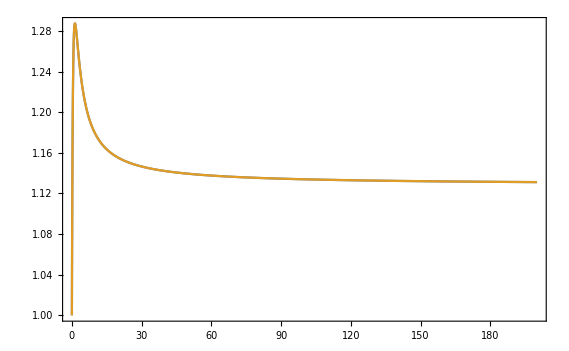

```mathematica
Plot[{g[x],c0 ChebyshevT[0,(x-k0)/(x+k0)]+Sum[c[[i]] ChebyshevT[i,(x-k0)/(x+k0)],{i,1,m}]},{x,0,200},WorkingPrecision->20, PlotRange->All,Frame->True]
```

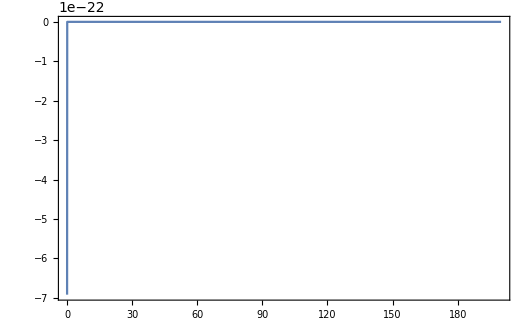

```mathematica
Plot[{c0 ChebyshevT[0,(x-k0)/(x+k0)]+Sum[c[[i]] ChebyshevT[i,(x-k0)/(x+k0)],{i,1,m}]-g[x]},{x,0,200},WorkingPrecision->20, PlotRange->All,Frame->True]
```